```mathematica
Sx=(h/Sqrt[2])*{{0,1,0},{1,0,1},{0,1,0}};
```

```mathematica
Sy=(h/Sqrt[2])*{{0,-I,0},{I,0,-I},{0,I,0}};
```

```mathematica
Sz=(h)*{{1,0,0},{0,0,0},{0,0,-1}};
```

```mathematica
ψ={1/2,Sqrt[2]/2,1/2};
```

```mathematica
Transpose[ψ].Sx.ψ
```

h

```mathematica
Transpose[ψ].Sy.ψ
```

0

```mathematica
Transpose[ψ].Sz.ψ
```

0

```mathematica
Transpose[ψ].Sx.Sx.ψ
```

h^2

```mathematica
Transpose[ψ].Sz.Sz.ψ
```

h^2/2

```mathematica
dSx=Transpose[ψ].Sx.Sx.ψ-(Transpose[ψ].Sx.ψ)^2
```

0

```mathematica
Transpose[ψ].(Sx.Sz-Sz.Sx).ψ
```

0

```mathematica
σz=(h/2)*PauliMatrix[3];
```

```mathematica
I3=IdentityMatrix[3];
```

```mathematica
I2=IdentityMatrix[2];
```

```mathematica
SZ=KroneckerProduct[σz,I3]+KroneckerProduct[I2,Sz];
```

```mathematica
Eigenvalues[SZ]
```

{-(3 h)/2,(3 h)/2,-h/2,-h/2,h/2,h/2}

```mathematica
Eigenvalues[Sz]
```

{-h/(√2),h/(√2),0}

```mathematica
Eigensystem[Sz]
```

{{-h,h,0},{{0,0,1},{1,0,0},{0,1,0}}}

```mathematica
Eigensystem[Sx]
```

{{-h,h,0},{{1,-√2,1},{1,√2,1},{-1,0,1}}}

```mathematica
Dot[{1,0,0},Normalize[{1,-Sqrt[2],1}]]
```

1/2

```mathematica
Dot[{1,0,0},Normalize[{1,Sqrt[2],1}]]
```

1/2

```mathematica
Dot[{1,0,0},Normalize[{-1,0,1}]]
```

-1/(√2)

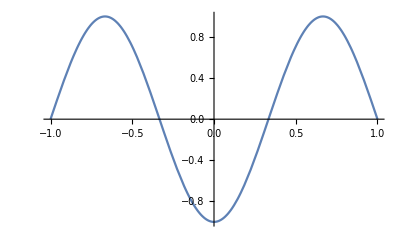

```mathematica
Plot[Sin[3*Pi*(y+1)/2],{y,-1,1}]
```

```mathematica
Integrate[Sin[n*Pi*(y+1)/2]^2,{y,-1,1}]
```

1-Sin[2 n π]/(2 n π)

```mathematica
N[Table[1+nx+(Pi^2/8)*ny^2,{nx,0,5},{ny,0,5}]]
```

{{1.,2.2337,5.9348,12.1033,20.7392,31.8425},{2.,3.2337,6.9348,13.1033,21.7392,32.8425},{3.,4.2337,7.9348,14.1033,22.7392,33.8425},{4.,5.2337,8.9348,15.1033,23.7392,34.8425},{5.,6.2337,9.9348,16.1033,24.7392,35.8425},{6.,7.2337,10.9348,17.1033,25.7392,36.8425}}

```mathematica
mat=Table[1/2+nx+(Pi^2/8)*ny^2,{nx,0,4},{ny,1,5}];
```

```mathematica
N[mat]//MatrixForm
```

(1.7337 | 5.4348 | 11.6033 | 20.2392 | 31.3425
2.7337 | 6.4348 | 12.6033 | 21.2392 | 32.3425
3.7337 | 7.4348 | 13.6033 | 22.2392 | 33.3425
4.7337 | 8.4348 | 14.6033 | 23.2392 | 34.3425
5.7337 | 9.4348 | 15.6033 | 24.2392 | 35.3425)

```mathematica
mat//MatrixForm
```

(1/2+π^2/8 | 1/2+π^2/2 | 1/2+(9 π^2)/8 | 1/2+2 π^2 | 1/2+(25 π^2)/8
3/2+π^2/8 | 3/2+π^2/2 | 3/2+(9 π^2)/8 | 3/2+2 π^2 | 3/2+(25 π^2)/8
5/2+π^2/8 | 5/2+π^2/2 | 5/2+(9 π^2)/8 | 5/2+2 π^2 | 5/2+(25 π^2)/8
7/2+π^2/8 | 7/2+π^2/2 | 7/2+(9 π^2)/8 | 7/2+2 π^2 | 7/2+(25 π^2)/8
9/2+π^2/8 | 9/2+π^2/2 | 9/2+(9 π^2)/8 | 9/2+2 π^2 | 9/2+(25 π^2)/8)